# 4基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

グラフ分析部分のみ、save済みグラフを読み込む。

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.910109312451676×10^9

#### 変数

```mathematica
date="20231030"
```

20231030

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/home/NII/togo-log/rcoslogs/"
```

/Volumes/home/NII/togo-log/rcoslogs/

```mathematica
vocdir=mountdir<>"voc"
```

/Volumes/home/NII/togo-log/rcoslogs/voc

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20231030.rcoslog0003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20231030.rcoslog0003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

21984119 312721328 10163914792 log-20231030.rcoslog0003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## Analysis

### Get graph

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231030/T=4/_story

```mathematica
Get[savedir<>"/storyGrIdxFlDs3.save"];
```

### Analysis 1 graph property

基本属性

エッジ:

```mathematica
(eltbl[4]=Table[EdgeList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{194612}

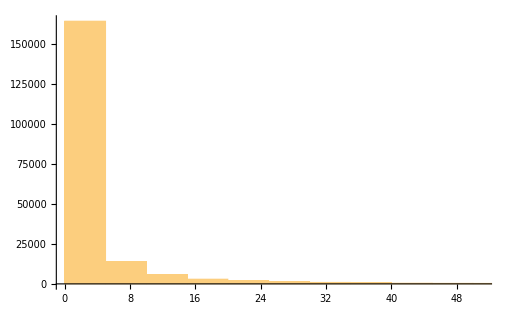

```mathematica
Histogram[Map[Length,eltbl[4]],{5}]
```

ノード:

```mathematica
(vltbl[4]=Table[VertexList[storyGrIdxFlDs3[4][[i]][[3]]],{i,Length[storyGrIdxFlDs3[4]]}])//Dimensions
```

{194612}

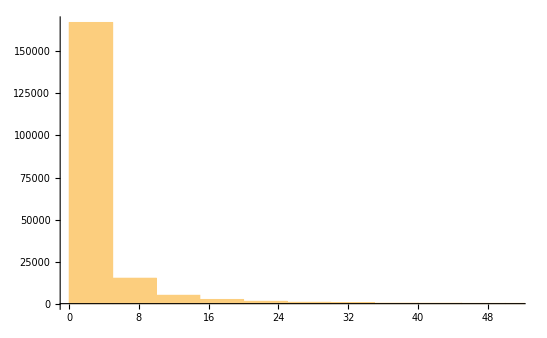

```mathematica
Histogram[Map[Length,vltbl[4]],{5}]
```

アクセス時刻:

```mathematica
(acct[4]=Map[#[[3,1]]&,eltbl[4],{2}])//Dimensions
```

{194612}

滞留時間：

```mathematica
(accspanMin[4]=Map[Max[#]-Min[#]&,acct[4]]/60)//Dimensions
```

{194612}

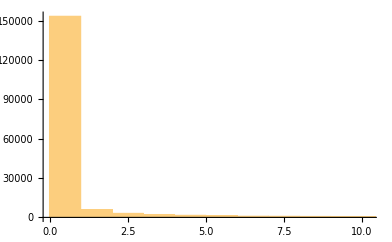

```mathematica
Histogram[accspanMin[4],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[4]=Map[Length,eltbl[4]]/Map[Length,vltbl[4]]//N)//Dimensions
```

{194612}

TV ratio :

```mathematica
(ratioTV[4]=acct[4]/Map[Length,vltbl[4]])//Dimensions
```

{194612}

TE ratio:

```mathematica
(ratioTE[4]=acct[4]/Map[Length,eltbl[4]])//Dimensions
```

{194612}

### Analysis 2 base interaction

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[4]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[4]])//Dimensions
```

Part::partw: Part {1,3} of {cir.nii.ac.jp} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧].

Part::partw: Part {1,3} of {www.bing.com} does not exist.

StringJoin::string: String expected at position 1 in StringJoin[{www.bing.com}⟦{1,3}⟧].

Part::partw: Part {1,3} of {www.bing.com} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[{www.bing.com}⟦{1,3}⟧].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{194612}

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[4]]//Union],True]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{127.0.0.1}⟦{1,3}⟧],RegularExpression[.*nii.ac.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{43,44,52,61,76,160,174,189,206,241,242,243,244,245,246,247,248,261,286,320,328,343,409,411,440,456,493,595,630,631,672,731,831,878,880,1131,1132,1194,1512,1611}

```mathematica
(Flatten[GrBases[4]]//Union)[[niidnpos]]
```

{http:ci.nii.ac.jp,http:cir.nii.ac.jp,http:dsr.nii.ac.jp,http:grafana.cs.rcos.nii.ac.jp,http:jdcat.jsps.go.jp,https:accounts.rdm.nii.ac.jp,https:analytics.la.lms.nii.ac.jp,https:auth.cir.nii.ac.jp,https:binder.cs.rcos.nii.ac.jp,https:ci.nii.ac.jp,https:ci.nii.ac.jp:443,https:cir.nii.ac.jp,https:cir.nii.ac.jp:443,https:cir-nii-ac-jp.ezproxy.tulips.tsukuba.ac.jp,https:cir-nii-ac-jp.lib-kansai-u.idm.oclc.org,https:cir-nii-ac-jp.musashino-u.remotexs.co,https:cir-nii-ac-jp.nagoya-u.idm.oclc.org,https:contents.nii.ac.jp,https:doshisha.repo.nii.ac.jp,https:feedback.cir.nii.ac.jp,https:fukuoka-u.repo.nii.ac.jp,https:ge.nii.ac.jp,https:idp.nii.ac.jp,https:idp.rdm.nii.ac.jp,https:jdcat.jsps.go.jp,https:jupyter.cs.rcos.nii.ac.jp,https:kogakkan.repo.nii.ac.jp,https:library.unii.ac.jp,https:lms.nii.ac.jp,https:lms.nii.ac.jp:443,https:meatwiki.nii.ac.jp,https:niph.repo.nii.ac.jp,https:openidp.nii.ac.jp,https:rcos.nii.ac.jp,https:rdm.nii.ac.jp,https:support.irdb.nii.ac.jp,https:support.nii.ac.jp,https:webfront.nii.ac.jp,https:www.nii.ac.jp,https:www.unii.ac.jp}

```mathematica
niigrp=".*\\.nii\\.ac\\.jp.*"
```

.*\.nii\.ac\.jp.*

```mathematica
(GrNiiBases[4]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[niigrp]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[4]])//Dimensions
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{cir.nii.ac.jp}⟦{1,3}⟧],RegularExpression[.*jdcat.jsps.go.jp.*]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[StringJoin[{www.bing.com}⟦{1,3}⟧],RegularExpression[.*\.nii\.ac\.jp.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{194612}

```mathematica
Map[Length,GrBases[4]]//Tally
```

{{2,173124},{1,21477},{3,11}}

```mathematica
Map[Length,GrNiiBases[4]]//Tally
```

{{1,139811},{2,54799},{3,2}}

```mathematica
(GrBasesTly[4]=Tally[GrBases[4]])//Dimensions
```

{1760,2}

```mathematica
(GrNiiBasesTly[4]=Tally[GrNiiBases[4]])//Dimensions
```

{43,2}

```mathematica
GrNiiBasesTly[4]//TableForm
```

https:cir.nii.ac.jp | 139328
https:ci.nii.ac.jp
https:cir.nii.ac.jp | 20811
http:ci.nii.ac.jp
https:cir.nii.ac.jp | 32330
https:cir.nii.ac.jp
https:support.nii.ac.jp | 155
https:cir.nii.ac.jp
https:www.nii.ac.jp | 9
https:lms.nii.ac.jp | 341
https:ci.nii.ac.jp:443
https:cir.nii.ac.jp | 86
https:lms.nii.ac.jp
https:www.nii.ac.jp | 4
https:lms.nii.ac.jp
https:meatwiki.nii.ac.jp | 1
https:cir.nii.ac.jp
https:idp.nii.ac.jp | 1
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp | 8
https:jdcat.jsps.go.jp | 44
https:jdcat.jsps.go.jp
https:www.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp | 3
http:cir.nii.ac.jp
https:cir.nii.ac.jp | 6
https:jupyter.cs.rcos.nii.ac.jp | 98
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 12
https:jupyter.cs.rcos.nii.ac.jp
https:rdm.nii.ac.jp | 12
https:idp.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:auth.cir.nii.ac.jp
https:cir.nii.ac.jp | 11
https:cir.nii.ac.jp
https:rcos.nii.ac.jp | 4
https:cir.nii.ac.jp
https:kogakkan.repo.nii.ac.jp | 1
https:cir.nii.ac.jp
https:niph.repo.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:lms.nii.ac.jp | 2
https:cir.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:accounts.rdm.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:fukuoka-u.repo.nii.ac.jp | 1
https:lms.nii.ac.jp
https:rcos.nii.ac.jp | 1
https:jupyter.cs.rcos.nii.ac.jp
https:openidp.nii.ac.jp | 8
https:idp.nii.ac.jp
https:lms.nii.ac.jp | 3
http:grafana.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 7
https:cir.nii.ac.jp
https:feedback.cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:lms.nii.ac.jp
https:www.nii.ac.jp | 2
https:cir.nii.ac.jp
https:contents.nii.ac.jp | 1
https:cir.nii.ac.jp
https:support.irdb.nii.ac.jp | 1
https:cir.nii.ac.jp
https:doshisha.repo.nii.ac.jp | 2
http:jdcat.jsps.go.jp
https:jdcat.jsps.go.jp | 2
https:analytics.la.lms.nii.ac.jp
https:lms.nii.ac.jp | 7
https:cir.nii.ac.jp
https:cir.nii.ac.jp:443 | 1291
https:lms.nii.ac.jp
https:lms.nii.ac.jp:443 | 8
http:dsr.nii.ac.jp
https:cir.nii.ac.jp | 1
https:cir.nii.ac.jp
https:webfront.nii.ac.jp | 1
https:cir.nii.ac.jp
https:ge.nii.ac.jp | 2

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

### Analysis 3 time series

```mathematica
accessFirst=(Cases[accessTime[4],x_/;x>0]//Min)
```

3.90761×10^9

```mathematica
accessLast=(Cases[accessTime[4],x_/;x>0]//Max)
```

3.9077×10^9

```mathematica
Sort[accessTime["ci"]]//Length
```

3310604

```mathematica
BC600["ci"]=BinCounts[Sort[accessTime["ci"]],{accessFirst,accessLast,60*10}]
```

{31322,31664,31994,33937,34408,34879,34539,33576,26245,33107,31023,30129,20330,13350,13961,13157,11913,13415,10999,11841,10195,10168,10181,10339,10050,11464,12201,12927,10442,9804,9400,9892,9603,11788,13351,13989,18410,14729,14540,14981,16107,16259,15161,15554,14029,14550,15096,14023,15242,14027,15748,14971,15404,22596,24747,24997,27453,28435,28469,26555,27396,28989,28047,28506,27588,27470,28745,29273,28794,32037,29988,27183,21811,14891,14229,15526,15073,14377,18550,17719,18783,19742,19684,19150,19032,19732,18637,18932,17900,22548,28747,31490,32386,34848,33494,31123,32327,28932,28201,27502,28079,26744,25443,25773,25128,24269,24139,23744,23706,23874,22528,19767,19067,19888,19321,20921,21643,22148,22093,21420,21262,26090,30700,30832,31182,30726,29613,30873,31035,32537,33212,33352,33067,33015,32826,32912,32313,33556,31748,33760,32615,33788,33593}

```mathematica
BC600["cs"]=BinCounts[Sort[accessTime["cs"]],{accessFirst,accessLast,60*10}]
```

{3,3,17,1,43,23,17,1,17,1,0,2,4,1,17,0,41,1,0,1,4710,220,1,0,1,3,17,0,41,0,1,1,19,0,1,1,1,0,17,0,42,0,1,3,20,1,8,1,0,1,159,60,48,53,61,73,82,1,7,89,56,1034,547,245,816,686,662,869,799,486,738,723,383,377,196,5,42,1,1,7,99,134,290,348,230,159,62,8,48,4,44,30,109,421,351,7,7,3,53,14,164,149,145,3,102,197,674,549,593,630,805,30,43,0,0,1,17,4,1,0,2,54,18,1,40,2,0,1,19,2,8,0,0,0,19,2,41,0,0,106,135,59,4}

```mathematica
BC600["la"]=BinCounts[Sort[accessTime["la"]],{accessFirst,accessLast,60*10}]
```

{166,145,676,132,160,15,163,386,26,82,124,369,2,20,68,285,148,431,16,57,0,0,1,0,0,0,6,3,0,84,14,7,159,138,142,185,159,140,125,63,160,196,228,161,123,6,3,2,0,45,44,5,131,140,330,301,748,1019,892,545,288,597,625,453,510,1148,1063,294,593,330,226,104,41,120,199,232,494,269,621,327,554,845,291,1225,1070,726,306,534,1739,964,616,844,1510,502,1579,493,522,1036,1378,1026,937,1766,859,264,904,1402,527,544,321,643,347,137,214,90,222,159,442,217,1559,812,955,446,590,486,630,539,1162,906,792,525,394,369,222,245,157,211,191,286,463,422,514,1275,434}

```mathematica
BC600["wk"]=BinCounts[Sort[accessTime["wk"]],{accessFirst,accessLast,60*10}]
```

{0,7,5,11,0,0,2,0,0,0,0,1,1,0,1,0,6,0,0,0,0,1,4,2,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,1,1,0,0,0,0,4,0,2,0,0,0,4,0,0,1,0,0,0,1,3,7,1,12,4,15,21,9,10,5,4,1,0,6,2,1,2,1,1,0,0,3,1,1,3,70,0,0,0,0,1,0,1,0,6,0,0,3,2,3,0,0,6,1,2,0,0,1,3,1,0,0,0,7,1,79,94,130,1,0,0,0,0,1,1,1,2,0,2,0,0,1,0,0,1,3,11,0,0,0,0,26,3}

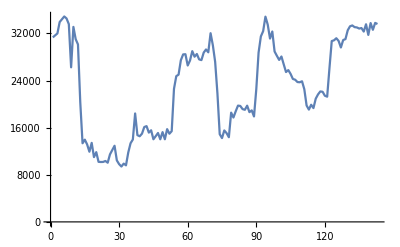

```mathematica
ListPlot[BC600["ci"],PlotRange->Full,Joined->True]
```

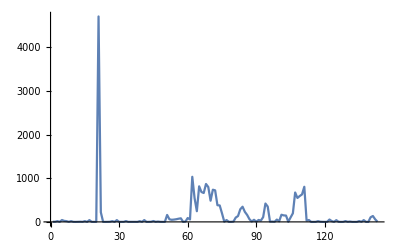

```mathematica
ListPlot[BC600["cs"],PlotRange->Full,Joined->True]
```

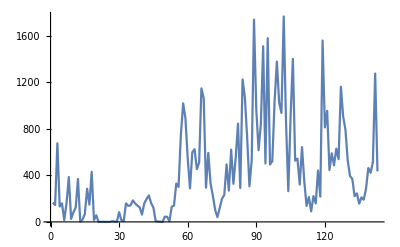

```mathematica
ListPlot[BC600["la"],PlotRange->Full,Joined->True]
```

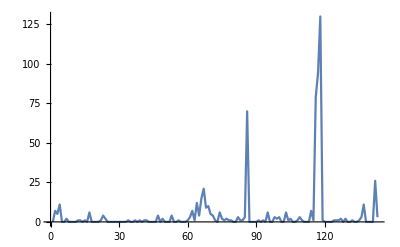

```mathematica
ListPlot[BC600["wk"],PlotRange->Full,Joined->True]
```

### Analysis 4 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[4]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{194612}

```mathematica
(ckanGrR[4]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{194612}

```mathematica
(ckanGrPR[4]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[4]],#,Null]&,storyGrIdxFlDs3[4]])//Dimensions
```

{194612}

```mathematica
(ckanGrPsel[4]=Cases[ckanGrP[4],{__},{1}])//Dimensions
```

{99,3}

```mathematica
ckanGrPselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
ckanGrPselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPsel[4]];
```

```mathematica
(ckanGrRsel[4]=Cases[ckanGrR[4],{__},{1}])//Dimensions
```

{10,3}

```mathematica
ckanGrRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
ckanGrRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrRsel[4]];
```

```mathematica
(ckanGrPRsel[4]=Cases[ckanGrPR[4],{__},{1}])//Dimensions
```

{101,3}

```mathematica
ckanGrPRselVL[4]=Map[VertexList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
ckanGrPRselEL[4]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[4]];
```

```mathematica
(ckanGrPRselHL[4]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[4]])//Dimensions
```

{101,3}

```mathematica
ckanGrPRVcount[4]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[4]]
```

{4,31,43,2,20,6,20,20,40,8,7,16,2,12,4,4,2,57,48,5,25,26,48,31,179,174,156,156,156,171,19,26,13,50,49,61,24,14,7,19,21,16,2,17,24,14,2,60,37,15,8,22,11,12,10,59,63,59,61,19,27,2,100,6,5,5,38,15,5,19,10,33,32,36,5,4,22,131,83,18,93,92,92,92,92,92,23,5,26,32,40,23,24,24,7,32,14,15,18,5,23}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[4]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[4]]
```

{0.,30406.,3754.,0.,1177.,504.,34757.,34750.,2090.,14369.,14340.,13142.,0.,1260.,59.,205.,0.,1148.,4235.,9.,37360.,37360.,795.,608.,42936.,36141.,36141.,36141.,41674.,37483.,23441.,988.,584.,19695.,19685.,31469.,675.,632.,120.,14569.,14569.,16510.,20.,1676.,556.,3947.,0.,40604.,30989.,4292.,519.,3557.,3213.,314.,232.,36383.,36393.,36383.,36383.,24958.,6908.,0.,2900.,128.,23.,33.,4538.,722.,25.,770.,431.,30066.,30011.,30011.,21404.,18.,360.,19004.,2961.,10090.,19218.,16619.,16602.,16602.,16602.,16602.,1760.,16.,83463.,1324.,2547.,1591.,1426.,3812.,47.,13372.,813.,6392.,1505.,7897.,1796.}

### Analysis 5 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[4]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[4]])//Dimensions
```

{101,3}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[4]]
```

{{1083,1},{5599,1},{6096,1},{11899,1},{13471,1},{14893,1},{15884,1},{15884,1},{16684,1},{16993,1},{16993,1},{18581,1},{22950,1},{28125,1},{28879,1},{31574,1},{33625,1},{35785,1},{36186,1},{40878,1},{49747,1},{49747,1},{53546,1},{53546,1},{54099,1},{54099,1},{54099,1},{54099,1},{54099,1},{54099,1},{55033,1},{55417,1},{56159,1},{56452,1},{56452,1},{56452,1},{57924,1},{57924,1},{61101,1},{61575,1},{61575,1},{64475,1},{66075,1},{68419,1},{69906,1},{71167,1},{75162,1},{78675,1},{78675,1},{79981,1},{83066,1},{90188,1},{92830,1},{96054,1},{97505,1},{98611,1},{98611,1},{98611,1},{98611,1},{98710,1},{99726,1},{100324,1},{100588,1},{100732,1},{102850,1},{102865,1},{103419,1},{103934,1},{104667,1},{105920,1},{107298,1},{107322,1},{107322,1},{107322,1},{107563,1},{107570,1},{107638,1},{110366,1},{111081,1},{113272,1},{113548,1},{113548,1},{113548,1},{113548,1},{113548,1},{113548,1},{114208,1},{114260,1},{116176,1},{118757,1},{120186,1},{140500,1},{140500,1},{142190,1},{146707,1},{147391,1},{148224,1},{148224,1},{151628,1},{151629,1},{154751,1}}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{4,31,43,2,20,6,20,20,40,8,7,16,2,12,4,4,2,57,48,5,25,26,48,31,179,174,156,156,156,171,19,26,13,50,49,61,24,14,7,19,21,16,2,17,24,14,2,60,37,15,8,22,11,12,10,59,63,59,61,19,27,2,100,6,5,5,38,15,5,19,10,33,32,36,5,4,22,131,83,18,93,92,92,92,92,92,23,5,26,32,40,23,24,24,7,32,14,15,18,5,23}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[4]]
```

{1,47,82,1,24,12,30,31,69,11,9,33,1,21,3,5,1,58,59,4,39,43,85,54,270,236,212,211,212,226,27,40,17,71,66,81,38,19,13,27,30,18,2,33,33,16,1,97,71,14,14,44,23,21,13,86,96,87,90,22,30,1,205,6,4,6,55,15,4,23,13,46,39,43,4,3,56,164,138,30,137,135,130,135,132,131,46,5,42,48,47,34,37,75,10,51,32,43,24,6,36}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[4]])//Dimensions
```

{101}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{0,400.967,20.6167,0,6.45,7.11667,492.017,492.017,13.6667,230.383,232.317,116.833,0,14.5,0.55,2.45,0,2.86667,30.4167,0.0833333,487.983,487.3,0.966667,0.966667,112.883,64.1833,64.1833,64.1833,92.2167,64.1833,214.517,2.76667,2.46667,128.233,128.283,150.217,1.26667,6.3,0.733333,135.633,134.95,226.417,0.333333,14.05,1.81667,29.15,0,134.25,200.833,65.85,5.2,12.0333,44.6,1.28333,1.16667,174.2,173.383,174.2,174.2,171.883,79.9833,0,3.6,0.8,0.15,0.2,40.35,7.11667,0.183333,5.78333,2.41667,293.517,293.367,243.667,187.55,0.216667,0.683333,51.3667,12.8333,65.3,72.8667,72.8667,72.8667,72.8667,72.8667,72.8667,8.6,0.133333,747.833,9.95,7.96667,4.61667,4.01667,32.05,0.3,189.733,2.51667,92.9667,12.0667,131.15,15.75}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{0.,30406.,3754.,0.,1177.,504.,34757.,34750.,2090.,14369.,14340.,13142.,0.,1260.,59.,205.,0.,1148.,4235.,9.,37360.,37360.,795.,608.,42936.,36141.,36141.,36141.,41674.,37483.,23441.,988.,584.,19695.,19685.,31469.,675.,632.,120.,14569.,14569.,16510.,20.,1676.,556.,3947.,0.,40604.,30989.,4292.,519.,3557.,3213.,314.,232.,36383.,36393.,36383.,36383.,24958.,6908.,0.,2900.,128.,23.,33.,4538.,722.,25.,770.,431.,30066.,30011.,30011.,21404.,18.,360.,19004.,2961.,10090.,19218.,16619.,16602.,16602.,16602.,16602.,1760.,16.,83463.,1324.,2547.,1591.,1426.,3812.,47.,13372.,813.,6392.,1505.,7897.,1796.}

```mathematica
staytimeCKAN/60
```

{0.,506.767,62.5667,0.,19.6167,8.4,579.283,579.167,34.8333,239.483,239.,219.033,0.,21.,0.983333,3.41667,0.,19.1333,70.5833,0.15,622.667,622.667,13.25,10.1333,715.6,602.35,602.35,602.35,694.567,624.717,390.683,16.4667,9.73333,328.25,328.083,524.483,11.25,10.5333,2.,242.817,242.817,275.167,0.333333,27.9333,9.26667,65.7833,0.,676.733,516.483,71.5333,8.65,59.2833,53.55,5.23333,3.86667,606.383,606.55,606.383,606.383,415.967,115.133,0.,48.3333,2.13333,0.383333,0.55,75.6333,12.0333,0.416667,12.8333,7.18333,501.1,500.183,500.183,356.733,0.3,6.,316.733,49.35,168.167,320.3,276.983,276.7,276.7,276.7,276.7,29.3333,0.266667,1391.05,22.0667,42.45,26.5167,23.7667,63.5333,0.783333,222.867,13.55,106.533,25.0833,131.617,29.9333}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[4]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[4]])//Dimensions
```

Part::partd: Part specification https://cir.nii.ac.jp/crid/1690576448918485632⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://cir.nii.ac.jp/crid/1690013498972408320⟦2⟧ is longer than depth of object.

Part::partd: Part specification https://cir.nii.ac.jp/crid/1690294973956971136⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{101}

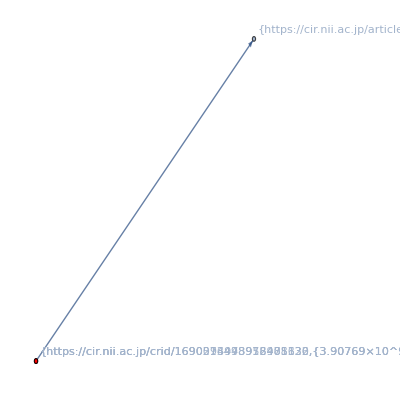

```mathematica
ckanGrPRselHLTL[4][[1]]
```

### Analysis 6 CKAN voc-graph

vocRlの読み込み：

```mathematica
vocRlFiles=FileNames[vocdir<>"/*.wl"]
```

{/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_path_action_wk_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_ci_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_cs_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_la_rl.wl,/Volumes/home/NII/togo-log/rcoslogs/voc/voc_ref_action_wk_rl.wl}

```mathematica
vocRlList=Map[Get,vocRlFiles];
```

```mathematica
(vocRl["all:path"]=Apply[Join,vocRlList])//Dimensions
```

{113}

```mathematica
vocRl["all:path"][[1]]
```

x_/;StringMatchQ[x,RegularExpression[https://cir.nii.ac.jp/]]→voc[ci:top]

===== /プログラム検討 =====

====== /引数 ======

```mathematica
gr=ckanGrPRselHLTL[4][[1]]
```

-Graphics-

```mathematica
rl=vocRl["all:path"];
```

====== 引数/ ======

====== /内部変数 ======

```mathematica
vl=VertexList[gr]
```

{{https://cir.nii.ac.jp/crid/1690576448918485632,{3.90769×10^9}},{https://cir.nii.ac.jp/crid/1690013498972408320,{3.90769×10^9}},{https://cir.nii.ac.jp/articles,{3.90769×10^9}},{https://cir.nii.ac.jp/crid/1690294973956971136,{3.90769×10^9}}}

```mathematica
vname=Map[#[[1]]&,vl]
```

{https://cir.nii.ac.jp/crid/1690576448918485632,https://cir.nii.ac.jp/crid/1690013498972408320,https://cir.nii.ac.jp/articles,https://cir.nii.ac.jp/crid/1690294973956971136}

```mathematica
vrename=(vname/.rl)
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

{voc[ci:detail],voc[ci:detail],voc[ci:search/articles],voc[ci:detail]}

```mathematica
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]]
```

{{https://cir.nii.ac.jp/crid/1690576448918485632,{3.90769×10^9}}→voc[ci:detail],{https://cir.nii.ac.jp/crid/1690013498972408320,{3.90769×10^9}}→voc[ci:detail],{https://cir.nii.ac.jp/articles,{3.90769×10^9}}→voc[ci:search/articles],{https://cir.nii.ac.jp/crid/1690294973956971136,{3.90769×10^9}}→voc[ci:detail]}

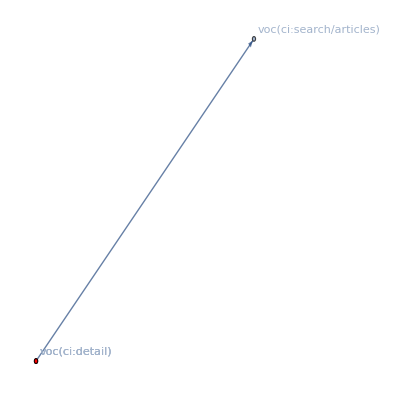

```mathematica
Graph[gr,VertexLabels->vrenameRl]
```

====== 内部変数/ ======

===== プログラム検討/ =====

```mathematica
toVocGraph[gr_,rl_]:=Module[{vl,vname,vrename,vrenameRl},
Print["it may cause StringMatchQ warn."];
vl=VertexList[gr];
vname=Map[#[[1]]&,vl];
vrename=(vname/.rl);
vrenameRl=Map[Apply[Rule,#]&,Transpose[{vl,vrename}]];
Graph[gr,VertexLabels->vrenameRl]
]
```

```mathematica
toVocGraph[ckanGrPRselHLTL[4][[1]],vocRl["all:path"]]
```

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

-Graphics-

it may cause StringMatchQ warn.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/ja]].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[List,RegularExpression[https://cir.nii.ac.jp/\?.*]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

it may cause StringMatchQ warn.

«97 more identical outputs»

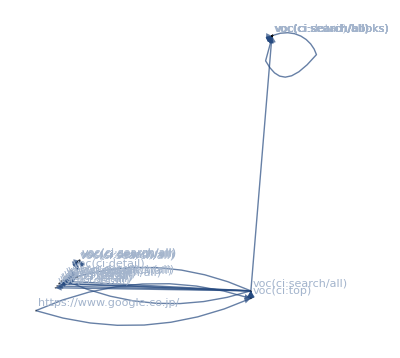
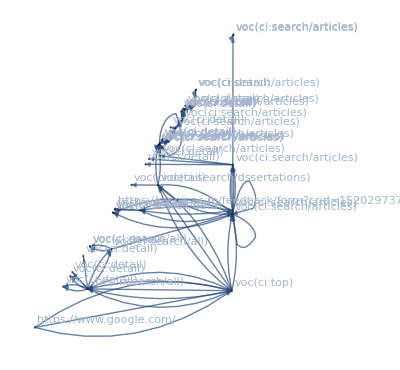
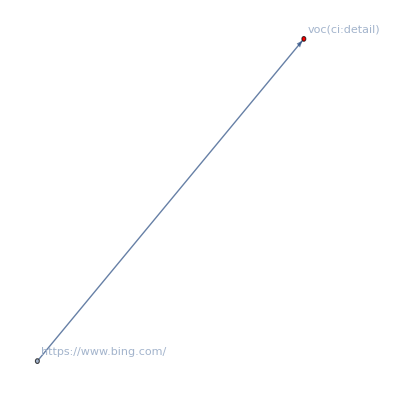
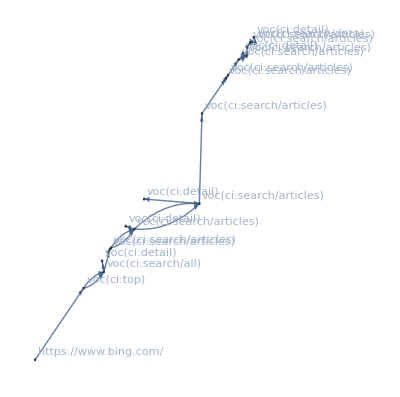
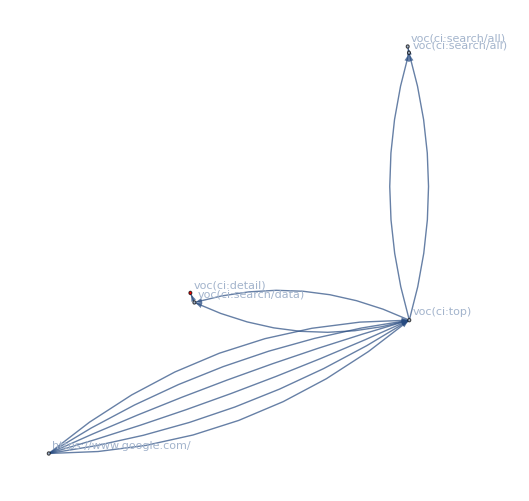
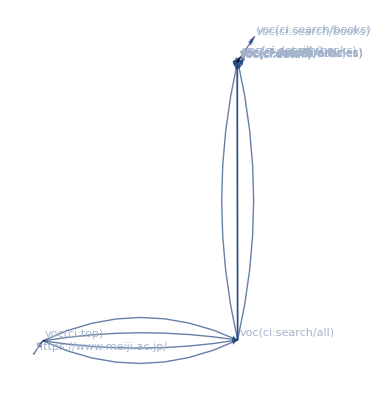
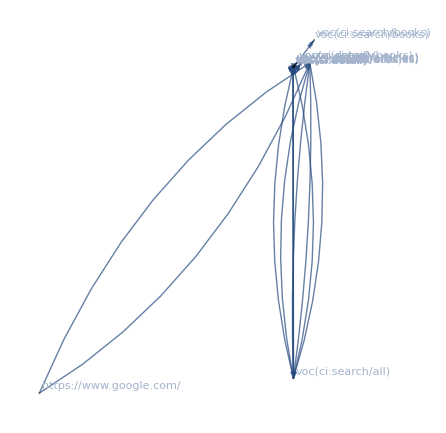
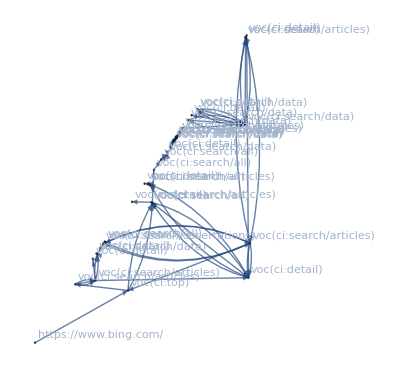
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
Map[toVocGraph[#,vocRl["all:path"]]&,ckanGrPRselHLTL[4]]//TableForm
```

### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLogLen[4]}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 21984119
3393969

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[4]//Length,ckanCridRLogPos[4]//Length,ckanCridPRLogPos[4]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 431
16
447 | 406
10
406

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[4]//Length,ckanGrPRselHL[4]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 194612
101

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
1
2
3
4
5
6
7
8
9
10
11
12
13
14
15
16
17
18
19
20
21
22
23
24
25
26
27
28
29
30
31
32
33
34
35
36
37
38
39
40
41
42
43
44
45
46
47
48
49
50
51
52
53
54
55
56
57
58
59
60
61
62
63
64
65
66
67
68
69
70
71
72
73
74
75
76
77
78
79
80
81
82
83
84
85
86
87
88
89
90
91
92
93
94
95
96
97
98
99
100
101 | 1083 | 1
5599 | 1
6096 | 1
11899 | 1
13471 | 1
14893 | 1
15884 | 1
15884 | 1
16684 | 1
16993 | 1
16993 | 1
18581 | 1
22950 | 1
28125 | 1
28879 | 1
31574 | 1
33625 | 1
35785 | 1
36186 | 1
40878 | 1
49747 | 1
49747 | 1
53546 | 1
53546 | 1
54099 | 1
54099 | 1
54099 | 1
54099 | 1
54099 | 1
54099 | 1
55033 | 1
55417 | 1
56159 | 1
56452 | 1
56452 | 1
56452 | 1
57924 | 1
57924 | 1
61101 | 1
61575 | 1
61575 | 1
64475 | 1
66075 | 1
68419 | 1
69906 | 1
71167 | 1
75162 | 1
78675 | 1
78675 | 1
79981 | 1
83066 | 1
90188 | 1
92830 | 1
96054 | 1
97505 | 1
98611 | 1
98611 | 1
98611 | 1
98611 | 1
98710 | 1
99726 | 1
100324 | 1
100588 | 1
100732 | 1
102850 | 1
102865 | 1
103419 | 1
103934 | 1
104667 | 1
105920 | 1
107298 | 1
107322 | 1
107322 | 1
107322 | 1
107563 | 1
107570 | 1
107638 | 1
110366 | 1
111081 | 1
113272 | 1
113548 | 1
113548 | 1
113548 | 1
113548 | 1
113548 | 1
113548 | 1
114208 | 1
114260 | 1
116176 | 1
118757 | 1
120186 | 1
140500 | 1
140500 | 1
142190 | 1
146707 | 1
147391 | 1
148224 | 1
148224 | 1
151628 | 1
151629 | 1
154751 | 1 | 4
31
43
2
20
6
20
20
40
8
7
16
2
12
4
4
2
57
48
5
25
26
48
31
179
174
156
156
156
171
19
26
13
50
49
61
24
14
7
19
21
16
2
17
24
14
2
60
37
15
8
22
11
12
10
59
63
59
61
19
27
2
100
6
5
5
38
15
5
19
10
33
32
36
5
4
22
131
83
18
93
92
92
92
92
92
23
5
26
32
40
23
24
24
7
32
14
15
18
5
23 | 1
47
82
1
24
12
30
31
69
11
9
33
1
21
3
5
1
58
59
4
39
43
85
54
270
236
212
211
212
226
27
40
17
71
66
81
38
19
13
27
30
18
2
33
33
16
1
97
71
14
14
44
23
21
13
86
96
87
90
22
30
1
205
6
4
6
55
15
4
23
13
46
39
43
4
3
56
164
138
30
137
135
130
135
132
131
46
5
42
48
47
34
37
75
10
51
32
43
24
6
36 | 0
400.967
20.6167
0
6.45
7.11667
492.017
492.017
13.6667
230.383
232.317
116.833
0
14.5
0.55
2.45
0
2.86667
30.4167
0.0833333
487.983
487.3
0.966667
0.966667
112.883
64.1833
64.1833
64.1833
92.2167
64.1833
214.517
2.76667
2.46667
128.233
128.283
150.217
1.26667
6.3
0.733333
135.633
134.95
226.417
0.333333
14.05
1.81667
29.15
0
134.25
200.833
65.85
5.2
12.0333
44.6
1.28333
1.16667
174.2
173.383
174.2
174.2
171.883
79.9833
0
3.6
0.8
0.15
0.2
40.35
7.11667
0.183333
5.78333
2.41667
293.517
293.367
243.667
187.55
0.216667
0.683333
51.3667
12.8333
65.3
72.8667
72.8667
72.8667
72.8667
72.8667
72.8667
8.6
0.133333
747.833
9.95
7.96667
4.61667
4.01667
32.05
0.3
189.733
2.51667
92.9667
12.0667
131.15
15.75 | 0.
506.767
62.5667
0.
19.6167
8.4
579.283
579.167
34.8333
239.483
239.
219.033
0.
21.
0.983333
3.41667
0.
19.1333
70.5833
0.15
622.667
622.667
13.25
10.1333
715.6
602.35
602.35
602.35
694.567
624.717
390.683
16.4667
9.73333
328.25
328.083
524.483
11.25
10.5333
2.
242.817
242.817
275.167
0.333333
27.9333
9.26667
65.7833
0.
676.733
516.483
71.5333
8.65
59.2833
53.55
5.23333
3.86667
606.383
606.55
606.383
606.383
415.967
115.133
0.
48.3333
2.13333
0.383333
0.55
75.6333
12.0333
0.416667
12.8333
7.18333
501.1
500.183
500.183
356.733
0.3
6.
316.733
49.35
168.167
320.3
276.983
276.7
276.7
276.7
276.7
29.3333
0.266667
1391.05
22.0667
42.45
26.5167
23.7667
63.5333
0.783333
222.867
13.55
106.533
25.0833
131.617
29.9333

### Export:CKAN impact

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[4]])//Dimensions
```

{101}

```mathematica
ckanELexp=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}];
```

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231030/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/home/NII/togo-log/rcoslogs/log/D=20231030/T=4/_story

```mathematica
Export["ckanedgelist.json",ckanELexp]
```

ckanedgelist.json

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.910109376584696×10^9

```mathematica
end-start
```

64.13302